```mathematica
q[t_] = -1/(2*Cos[t])
```

-Sec[t]/2

```mathematica
r[t_] = (1 - 4*Cos[t])^(1/2)
```

√(1-4 Cos[t])

```mathematica
fmid[k_,t_] = (Sin[(k+2)*t]/Sin[t])*(1 + r[t]*q[t] + (r[t] + q[t])*Cos[t]) + (r[t] - q[t])*Cos[(k+2)t]
```

Cos[(2+k) t] (√(1-4 Cos[t])+Sec[t]/2)+Csc[t] (1+Cos[t] (√(1-4 Cos[t])-Sec[t]/2)-1/2 √(1-4 Cos[t]) Sec[t]) Sin[(2+k) t]

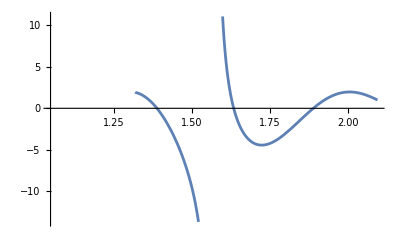

```mathematica
Plot[fmid[8,t], {t, π/3+10^-10, (2*π)/3-10^-10}]
```

```mathematica
Series[1/((1-t)*(1+t^2+z*t^3)), {t,0,90}]
```

1+t-z t^3+(1-z) t^4+(1+z) t^5+(z+z^2) t^6+(-2 z+z^2) t^7+(1-2 z-2 z^2) t^8+(1+2 z-2 z^2-z^3) t^9+(2 z+4 z^2-z^3) t^10+(-3 z+4 z^2+3 z^3) t^11+(1-3 z-6 z^2+3 z^3+z^4) t^12+(1+3 z-6 z^2-7 z^3+z^4) t^13+(3 z+9 z^2-7 z^3-4 z^4) t^14+(-4 z+9 z^2+13 z^3-4 z^4-z^5) t^15+(1-4 z-12 z^2+13 z^3+11 z^4-z^5) t^16+(1+4 z-12 z^2-22 z^3+11 z^4+5 z^5) t^17+(4 z+16 z^2-22 z^3-24 z^4+5 z^5+z^6) t^18+(-5 z+16 z^2+34 z^3-24 z^4-16 z^5+z^6) t^19+(1-5 z-20 z^2+34 z^3+46 z^4-16 z^5-6 z^6) t^20+(1+5 z-20 z^2-50 z^3+46 z^4+40 z^5-6 z^6-z^7) t^21+(5 z+25 z^2-50 z^3-80 z^4+40 z^5+22 z^6-z^7) t^22+(-6 z+25 z^2+70 z^3-80 z^4-86 z^5+22 z^6+7 z^7) t^23+(1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8) t^24+(1+6 z-30 z^2-95 z^3+130 z^4+166 z^5-62 z^6-29 z^7+z^8) t^25+(6 z+36 z^2-95 z^3-200 z^4+166 z^5+148 z^6-29 z^7-8 z^8) t^26+(-7 z+36 z^2+125 z^3-200 z^4-296 z^5+148 z^6+91 z^7-8 z^8-z^9) t^27+(1-7 z-42 z^2+125 z^3+295 z^4-296 z^5-314 z^6+91 z^7+37 z^8-z^9) t^28+(1+7 z-42 z^2-161 z^3+295 z^4+496 z^5-314 z^6-239 z^7+37 z^8+9 z^9) t^29+(7 z+49 z^2-161 z^3-420 z^4+496 z^5+610 z^6-239 z^7-128 z^8+9 z^9+z^10) t^30+(-8 z+49 z^2+203 z^3-420 z^4-791 z^5+610 z^6+553 z^7-128 z^8-46 z^9+z^10) t^31+(1-8 z-56 z^2+203 z^3+581 z^4-791 z^5-1106 z^6+553 z^7+367 z^8-46 z^9-10 z^10) t^32+(1+8 z-56 z^2-252 z^3+581 z^4+1211 z^5-1106 z^6-1163 z^7+367 z^8+174 z^9-10 z^10-z^11) t^33+(8 z+64 z^2-252 z^3-784 z^4+1211 z^5+1897 z^6-1163 z^7-920 z^8+174 z^9+56 z^10-z^11) t^34+(-9 z+64 z^2+308 z^3-784 z^4-1792 z^5+1897 z^6+2269 z^7-920 z^8-541 z^9+56 z^10+11 z^11) t^35+(1-9 z-72 z^2+308 z^3+1036 z^4-1792 z^5-3108 z^6+2269 z^7+2083 z^8-541 z^9-230 z^10+11 z^11+z^12) t^36+(1+9 z-72 z^2-372 z^3+1036 z^4+2576 z^5-3108 z^6-4166 z^7+2083 z^8+1461 z^9-230 z^10-67 z^11+z^12) t^37+(9 z+81 z^2-372 z^3-1344 z^4+2576 z^5+4900 z^6-4166 z^7-4352 z^8+1461 z^9+771 z^10-67 z^11-12 z^12) t^38+(-10 z+81 z^2+444 z^3-1344 z^4-3612 z^5+4900 z^6+7274 z^7-4352 z^8-3544 z^9+771 z^10+297 z^11-12 z^12-z^13) t^39+(1-10 z-90 z^2+444 z^3+1716 z^4-3612 z^5-7476 z^6+7274 z^7+8518 z^8-3544 z^9-2232 z^10+297 z^11+79 z^12-z^13) t^40+(1+10 z-90 z^2-525 z^3+1716 z^4+4956 z^5-7476 z^6-12174 z^7+8518 z^8+7896 z^9-2232 z^10-1068 z^11+79 z^12+13 z^13) t^41+(10 z+100 z^2-525 z^3-2160 z^4+4956 z^5+11088 z^6-12174 z^7-15792 z^8+7896 z^9+5776 z^10-1068 z^11-376 z^12+13 z^13+z^14) t^42+(-11 z+100 z^2+615 z^3-2160 z^4-6672 z^5+11088 z^6+19650 z^7-15792 z^8-16414 z^9+5776 z^10+3300 z^11-376 z^12-92 z^13+z^14) t^43+(1-11 z-110 z^2+615 z^3+2685 z^4-6672 z^5-16044 z^6+19650 z^7+27966 z^8-16414 z^9-13672 z^10+3300 z^11+1444 z^12-92 z^13-14 z^14) t^44+(1+11 z-110 z^2-715 z^3+2685 z^4+8832 z^5-16044 z^6-30738 z^7+27966 z^8+32206 z^9-13672 z^10-9076 z^11+1444 z^12+468 z^13-14 z^14-z^15) t^45+(11 z+121 z^2-715 z^3-3300 z^4+8832 z^5+22716 z^6-30738 z^7-47616 z^8+32206 z^9+30086 z^10-9076 z^11-4744 z^12+468 z^13+106 z^14-z^15) t^46+(-12 z+121 z^2+825 z^3-3300 z^4-11517 z^5+22716 z^6+46782 z^7-47616 z^8-60172 z^9+30086 z^10+22748 z^11-4744 z^12-1912 z^13+106 z^14+15 z^15) t^47+(1-12 z-132 z^2+825 z^3+4015 z^4-11517 z^5-31548 z^6+46782 z^7+78354 z^8-60172 z^9-62292 z^10+22748 z^11+13820 z^12-1912 z^13-574 z^14+15 z^15+z^16) t^48+(1+12 z-132 z^2-946 z^3+4015 z^4+14817 z^5-31548 z^6-69498 z^7+78354 z^8+107788 z^9-62292 z^10-52834 z^11+13820 z^12+6656 z^13-574 z^14-121 z^15+z^16) t^49+(12 z+144 z^2-946 z^3-4840 z^4+14817 z^5+43065 z^6-69498 z^7-125136 z^8+107788 z^9+122464 z^10-52834 z^11-36568 z^12+6656 z^13+2486 z^14-121 z^15-16 z^16) t^50+(-13 z+144 z^2+1078 z^3-4840 z^4-18832 z^5+43065 z^6+101046 z^7-125136 z^8-186142 z^9+122464 z^10+115126 z^11-36568 z^12-20476 z^13+2486 z^14+695 z^15-16 z^16-z^17) t^51+(1-13 z-156 z^2+1078 z^3+5786 z^4-18832 z^5-57882 z^6+101046 z^7+194634 z^8-186142 z^9-230252 z^10+115126 z^11+89402 z^12-20476 z^13-9142 z^14+695 z^15+137 z^16-z^17) t^52+(1+13 z-156 z^2-1222 z^3+5786 z^4+23672 z^5-57882 z^6-144111 z^7+194634 z^8+311278 z^9-230252 z^10-237590 z^11+89402 z^12+57044 z^13-9142 z^14-3181 z^15+137 z^16+17 z^17) t^53+(13 z+169 z^2-1222 z^3-6864 z^4+23672 z^5+76714 z^6-144111 z^7-295680 z^8+311278 z^9+416394 z^10-237590 z^11-204528 z^12+57044 z^13+29618 z^14-3181 z^15-832 z^16+17 z^17+z^18) t^54+(-14 z+169 z^2+1378 z^3-6864 z^4-29458 z^5+76714 z^6+201993 z^7-295680 z^8-505912 z^9+416394 z^10+467842 z^11-204528 z^12-146446 z^13+29618 z^14+12323 z^15-832 z^16-154 z^17+z^18) t^55+(1-14 z-182 z^2+1378 z^3+8086 z^4-29458 z^5-100386 z^6+201993 z^7+439791 z^8-505912 z^9-727672 z^10+467842 z^11+442118 z^12-146446 z^13-86662 z^14+12323 z^15+4013 z^16-154 z^17-18 z^18) t^56+(1+14 z-182 z^2-1547 z^3+8086 z^4+36322 z^5-100386 z^6-278707 z^7+439791 z^8+801592 z^9-727672 z^10-884236 z^11+442118 z^12+350974 z^13-86662 z^14-41941 z^15+4013 z^16+986 z^17-18 z^18-z^19) t^57+(14 z+196 z^2-1547 z^3-9464 z^4+36322 z^5+129844 z^6-278707 z^7-641784 z^8+801592 z^9+1233584 z^10-884236 z^11-909960 z^12+350974 z^13+233108 z^14-41941 z^15-16336 z^16+986 z^17+172 z^18-z^19) t^58+(-15 z+196 z^2+1729 z^3-9464 z^4-44408 z^5+129844 z^6+379093 z^7-641784 z^8-1241383 z^9+1233584 z^10+1611908 z^11-909960 z^12-793092 z^13+233108 z^14+128603 z^15-16336 z^16-4999 z^17+172 z^18+19 z^19) t^59+(1-15 z-210 z^2+1729 z^3+11011 z^4-44408 z^5-166166 z^6+379093 z^7+920491 z^8-1241383 z^9-2035176 z^10+1611908 z^11+1794196 z^12-793092 z^13-584082 z^14+128603 z^15+58277 z^16-4999 z^17-1158 z^18+19 z^19+z^20) t^60+(1+15 z-210 z^2-1925 z^3+11011 z^4+53872 z^5-166166 z^6-508937 z^7+920491 z^8+1883167 z^9-2035176 z^10-2845492 z^11+1794196 z^12+1703052 z^13-584082 z^14-361711 z^15+58277 z^16+21335 z^17-1158 z^18-191 z^19+z^20) t^61+(15 z+225 z^2-1925 z^3-12740 z^4+53872 z^5+210574 z^6-508937 z^7-1299584 z^8+1883167 z^9+3276559 z^10-2845492 z^11-3406104 z^12+1703052 z^13+1377174 z^14-361711 z^15-186880 z^16+21335 z^17+6157 z^18-191 z^19-20 z^20) t^62+(-16 z+225 z^2+2135 z^3-12740 z^4-64883 z^5+210574 z^6+675103 z^7-1299584 z^8-2803658 z^9+3276559 z^10+4880668 z^11-3406104 z^12-3497248 z^13+1377174 z^14+945793 z^15-186880 z^16-79612 z^17+6157 z^18+1349 z^19-20 z^20-z^21) t^63+(1-16 z-240 z^2+2135 z^3+14665 z^4-64883 z^5-264446 z^6+675103 z^7+1808521 z^8-2803658 z^9-5159726 z^10+4880668 z^11+6251596 z^12-3497248 z^13-3080226 z^14+945793 z^15+548591 z^16-79612 z^17-27492 z^18+1349 z^19+211 z^20-z^21) t^64+(1+16 z-240 z^2-2360 z^3+14665 z^4+77623 z^5-264446 z^6-885677 z^7+1808521 z^8+4103242 z^9-5159726 z^10-8157227 z^11+6251596 z^12+6903352 z^13-3080226 z^14-2322967 z^15+548591 z^16+266492 z^17-27492 z^18-7506 z^19+211 z^20+21 z^21) t^65+(16 z+256 z^2-2360 z^3-16800 z^4+77623 z^5+329329 z^6-885677 z^7-2483624 z^8+4103242 z^9+7963384 z^10-8157227 z^11-11132264 z^12+6903352 z^13+6577474 z^14-2322967 z^15-1494384 z^16+266492 z^17+107104 z^18-7506 z^19-1560 z^20+21 z^21+z^22) t^66+(-17 z+256 z^2+2600 z^3-16800 z^4-92288 z^5+329329 z^6+1150123 z^7-2483624 z^8-5911763 z^9+7963384 z^10+13316953 z^11-11132264 z^12-13154948 z^13+6577474 z^14+5403193 z^15-1494384 z^16-815083 z^17+107104 z^18+34998 z^19-1560 z^20-232 z^21+z^22) t^67+(1-17 z-272 z^2+2600 z^3+19160 z^4-92288 z^5-406952 z^6+1150123 z^7+3369301 z^8-5911763 z^9-12066626 z^10+13316953 z^11+19289491 z^12-13154948 z^13-13480826 z^14+5403193 z^15+3817351 z^16-815083 z^17-373596 z^18+34998 z^19+9066 z^20-232 z^21-22 z^22) t^68+(1+17 z-272 z^2-2856 z^3+19160 z^4+109088 z^5-406952 z^6-1479452 z^7+3369301 z^8+8395387 z^9-12066626 z^10-21280337 z^11+19289491 z^12+24287212 z^13-13480826 z^14-11980667 z^15+3817351 z^16+2309467 z^17-373596 z^18-142102 z^19+9066 z^20+1792 z^21-22 z^22-z^23) t^69+(17 z+289 z^2-2856 z^3-21760 z^4+109088 z^5+499240 z^6-1479452 z^7-4519424 z^8+8395387 z^9+17978389 z^10-21280337 z^11-32606444 z^12+24287212 z^13+26635774 z^14-11980667 z^15-9220544 z^16+2309467 z^17+1188679 z^18-142102 z^19-44064 z^20+1792 z^21+254 z^22-z^23) t^70+(-18 z+289 z^2+3128 z^3-21760 z^4-128248 z^5+499240 z^6+1886404 z^7-4519424 z^8-11764688 z^9+17978389 z^10+33346963 z^11-32606444 z^12-43576703 z^13+26635774 z^14+25461493 z^15-9220544 z^16-6126818 z^17+1188679 z^18+515698 z^19-44064 z^20-10858 z^21+254 z^22+23 z^23) t^71+(1-18 z-306 z^2+3128 z^3+24616 z^4-128248 z^5-608328 z^6+1886404 z^7+5998876 z^8-11764688 z^9-26373776 z^10+33346963 z^11+53886781 z^12-43576703 z^13-50922986 z^14+25461493 z^15+21201211 z^16-6126818 z^17-3498146 z^18+515698 z^19+186166 z^20-10858 z^21-2046 z^22+23 z^23+z^24) t^72+(1+18 z-306 z^2-3417 z^3+24616 z^4+150008 z^5-608328 z^6-2385644 z^7+5998876 z^8+16284112 z^9-26373776 z^10-51325352 z^11+53886781 z^12+76183147 z^13-50922986 z^14-52097267 z^15+21201211 z^16+15347362 z^17-3498146 z^18-1704377 z^19+186166 z^20+54922 z^21-2046 z^22-277 z^23+z^24) t^73+(18 z+324 z^2-3417 z^3-27744 z^4+150008 z^5+736576 z^6-2385644 z^7-7885280 z^8+16284112 z^9+38138464 z^10-51325352 z^11-87233744 z^12+76183147 z^13+94499689 z^14-52097267 z^15-46662704 z^16+15347362 z^17+9624964 z^18-1704377 z^19-701864 z^20+54922 z^21+12904 z^22-277 z^23-24 z^24) t^74+(-19 z+324 z^2+3723 z^3-27744 z^4-174624 z^5+736576 z^6+2993972 z^7-7885280 z^8-22282988 z^9+38138464 z^10+77699128 z^11-87233744 z^12-130069928 z^13+94499689 z^14+103020253 z^15-46662704 z^16-36548573 z^17+9624964 z^18+5202523 z^19-701864 z^20-241088 z^21+12904 z^22+2323 z^23-24 z^24-z^25) t^75+(1-19 z-342 z^2+3723 z^3+31161 z^4-174624 z^5-886584 z^6+2993972 z^7+10270924 z^8-22282988 z^9-54422576 z^10+77699128 z^11+138559096 z^12-130069928 z^13-170682836 z^14+103020253 z^15+98759971 z^16-36548573 z^17-24972326 z^18+5202523 z^19+2406241 z^20-241088 z^21-67826 z^22+2323 z^23+301 z^24-z^25) t^76+(1+19 z-342 z^2-4047 z^3+31161 z^4+202368 z^5-886584 z^6-3730548 z^7+10270924 z^8+30168268 z^9-54422576 z^10-115837592 z^11+138559096 z^12+217303672 z^13-170682836 z^14-197519942 z^15+98759971 z^16+83211277 z^17-24972326 z^18-14827487 z^19+2406241 z^20+942952 z^21-67826 z^22-15227 z^23+301 z^24+25 z^25) t^77+(19 z+361 z^2-4047 z^3-34884 z^4+202368 z^5+1061208 z^6-3730548 z^7-13264896 z^8+30168268 z^9+76705564 z^10-115837592 z^11-216258224 z^12+217303672 z^13+300752764 z^14-197519942 z^15-201780224 z^16+83211277 z^17+61520899 z^18-14827487 z^19-7608764 z^20+942952 z^21+308914 z^22-15227 z^23-2624 z^24+25 z^25+z^26) t^78+(-20 z+361 z^2+4389 z^3-34884 z^4-233529 z^5+1061208 z^6+4617132 z^7-13264896 z^8-40439192 z^9+76705564 z^10+170260168 z^11-216258224 z^12-355862768 z^13+300752764 z^14+368202778 z^15-201780224 z^16-181971248 z^17+61520899 z^18+39799813 z^19-7608764 z^20-3349193 z^21+308914 z^22+83053 z^23-2624 z^24-326 z^25+z^26) t^79+(1-20 z-380 z^2+4389 z^3+38931 z^4-233529 z^5-1263576 z^6+4617132 z^7+16995444 z^8-40439192 z^9-106873832 z^10+170260168 z^11+332095816 z^12-355862768 z^13-518056436 z^14+368202778 z^15+399300166 z^16-181971248 z^17-144732176 z^18+39799813 z^19+22436251 z^20-3349193 z^21-1251866 z^22+83053 z^23+17851 z^24-326 z^25-26 z^26) t^80+(1+20 z-380 z^2-4750 z^3+38931 z^4+268413 z^5-1263576 z^6-5678340 z^7+16995444 z^8+53704088 z^9-106873832 z^10-246965732 z^11+332095816 z^12+572120992 z^13-518056436 z^14-668955542 z^15+399300166 z^16+383751472 z^17-144732176 z^18-101320712 z^19+22436251 z^20+10957957 z^21-1251866 z^22-391967 z^23+17851 z^24+2950 z^25-26 z^26-z^27) t^81+(20 z+400 z^2-4750 z^3-43320 z^4+268413 z^5+1497105 z^6-5678340 z^7-21612576 z^8+53704088 z^9+147313024 z^10-246965732 z^11-502355984 z^12+572120992 z^13+873919204 z^14-668955542 z^15-767502944 z^16+383751472 z^17+326703424 z^18-101320712 z^19-62236064 z^20+10957957 z^21+4601059 z^22-391967 z^23-100904 z^24+2950 z^25+352 z^26-z^27) t^82+(-21 z+400 z^2+5130 z^3-43320 z^4-307344 z^5+1497105 z^6+6941916 z^7-21612576 z^8-70699532 z^9+147313024 z^10+353839564 z^11-502355984 z^12-904216808 z^13+873919204 z^14+1187011978 z^15-767502944 z^16-783051638 z^17+326703424 z^18+246052888 z^19-62236064 z^20-33394208 z^21+4601059 z^22+1643833 z^23-100904 z^24-20801 z^25+352 z^26+27 z^27) t^83+(1-21 z-420 z^2+5130 z^3+48070 z^4-307344 z^5-1765518 z^6+6941916 z^7+27290916 z^8-70699532 z^9-201017112 z^10+353839564 z^11+749321716 z^12-904216808 z^13-1446040196 z^14+1187011978 z^15+1436458486 z^16-783051638 z^17-710454896 z^18+246052888 z^19+163556776 z^20-33394208 z^21-15559016 z^22+1643833 z^23+492871 z^24-20801 z^25-3302 z^26+27 z^27+z^28) t^84+(1+21 z-420 z^2-5530 z^3+48070 z^4+350664 z^5-1765518 z^6-8439021 z^7+27290916 z^8+92312108 z^9-201017112 z^10-501152588 z^11+749321716 z^12+1406572792 z^13-1446040196 z^14-2060931182 z^15+1436458486 z^16+1550554582 z^17-710454896 z^18-572756312 z^19+163556776 z^20+95630272 z^21-15559016 z^22-6244892 z^23+492871 z^24+121705 z^25-3302 z^26-379 z^27+z^28) t^85+(21 z+441 z^2-5530 z^3-53200 z^4+350664 z^5+2072862 z^6-8439021 z^7-34232832 z^8+92312108 z^9+271716644 z^10-501152588 z^11-1103161280 z^12+1406572792 z^13+2350257004 z^14-2060931182 z^15-2623470464 z^16+1550554582 z^17+1493506534 z^18-572756312 z^19-409609664 z^20+95630272 z^21+48953224 z^22-6244892 z^23-2136704 z^24+121705 z^25+24103 z^26-379 z^27-28 z^28) t^86+(-22 z+441 z^2+5950 z^3-53200 z^4-398734 z^5+2072862 z^6+10204539 z^7-34232832 z^8-119603024 z^9+271716644 z^10+702169700 z^11-1103161280 z^12-2155894508 z^13+2350257004 z^14+3506971378 z^15-2623470464 z^16-2987013068 z^17+1493506534 z^18+1283211208 z^19-409609664 z^20-259187048 z^21+48953224 z^22+21803908 z^23-2136704 z^24-614576 z^25+24103 z^26+3681 z^27-28 z^28-z^29) t^87+(1-22 z-462 z^2+5950 z^3+58730 z^4-398734 z^5-2423526 z^6+10204539 z^7+42671853 z^8-119603024 z^9-364028752 z^10+702169700 z^11+1604313868 z^12-2155894508 z^13-3756829796 z^14+3506971378 z^15+4684401646 z^16-2987013068 z^17-3044061116 z^18+1283211208 z^19+982365976 z^20-259187048 z^21-144583496 z^22+21803908 z^23+8381596 z^24-614576 z^25-145808 z^26+3681 z^27+407 z^28-z^29) t^88+(1+22 z-462 z^2-6391 z^3+58730 z^4+451934 z^5-2423526 z^6-12277401 z^7+42671853 z^8+153835856 z^9-364028752 z^10-973886344 z^11+1604313868 z^12+3259055788 z^13-3756829796 z^14-5857228382 z^15+4684401646 z^16+5610483532 z^17-3044061116 z^18-2776717742 z^19+982365976 z^20+668796712 z^21-144583496 z^22-70757132 z^23+8381596 z^24+2751280 z^25-145808 z^26-27784 z^27+407 z^28+29 z^29) t^89+(22 z+484 z^2-6391 z^3-64680 z^4+451934 z^5+2822260 z^6-12277401 z^7-52876392 z^8+153835856 z^9+483631776 z^10-973886344 z^11-2306483568 z^12+3259055788 z^13+5912724304 z^14-5857228382 z^15-8191373024 z^16+5610483532 z^17+6031074184 z^18-2776717742 z^19-2265577184 z^20+668796712 z^21+403770544 z^22-70757132 z^23-30185504 z^24+2751280 z^25+760384 z^26-27784 z^27-4088 z^28+29 z^29+z^30) t^90+O[t]^91

```mathematica
Series[1/((1-t)*(1+t^2)),{t,0,90}]
```

1+t+t^4+t^5+t^8+t^9+t^12+t^13+t^16+t^17+t^20+t^21+t^24+t^25+t^28+t^29+t^32+t^33+t^36+t^37+t^40+t^41+t^44+t^45+t^48+t^49+t^52+t^53+t^56+t^57+t^60+t^61+t^64+t^65+t^68+t^69+t^72+t^73+t^76+t^77+t^80+t^81+t^84+t^85+t^88+t^89+O[t]^91

```mathematica
CountRoots[SeriesCoefficient[1/((1-t)*(1+t^2+z*t^3)),{t,0,90}],{z,-10^10, 10^10}]
```

30

```mathematica
SeriesCoefficient[1/((1-t)*(1+t^2+z*t^3)),{t,0,21}]
```

1+5 z-20 z^2-50 z^3+46 z^4+40 z^5-6 z^6-z^7

```mathematica
roots = z /. NSolve[SeriesCoefficient[1/((1-t)*(1+t^2+z*t^3)),{t,0,12}] == 0]
```

{-4.23607,-0.618034,0.236068,1.61803}

```mathematica
RootTestFunction[k_,f_] := (SeriesCoefficient[f,{t,0,k}]; roots=z/.NSolve[SeriesCoefficient[f,{t,0,k}]==0]);
```

```mathematica
RootTestFunction
```

RootTestFunction

```mathematica
f[t_] = 1/((1-t)*(1 + t^2+z*t^3))
```

1/((1-t) (1+t^2+t^3 z))

```mathematica
RootTestFunction[10,f[t]]
```

{-0.44949,0.,4.44949}

```mathematica
RootTestFunction[k_, f_]:={coefs->SeriesCoefficient[f,{t,0,k}], rootvals -> List[z/.NSolve[SeriesCoefficient[f,{t,0,k}]==0]] , numroots -> Length[rootvals]}
```

```mathematica
RootTestFunction[10, f[t]]
```

{coefs→2 z+4 z^2-z^3,rootvals→{{-0.44949,0.,4.44949}},numroots→0}

```mathematica
RootTestFunction2[k_,f_]:=Module[
{coefs, rootvals, numroots},
coefs = SeriesCoefficient[f,{t,0,k}];
rootvals = {Re[#], Im[#]} &/@(z/.NSolve[SeriesCoefficient[f,{t,0,k}]==0]) ;
numroots = Length[rootvals];
{coefs, rootvals, numroots}
];
```

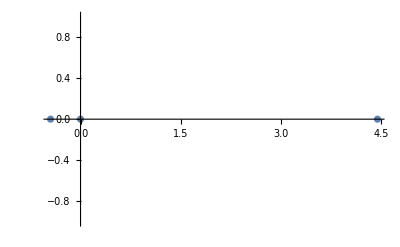
{(2 z+4 z^2-z^3) -Graphics-,{{-0.44949 -Graphics-,0},{0.,0},{4.44949 -Graphics-,0}},3 -Graphics-}

```mathematica
RootTestFunction2[10, f[t]]
```

```mathematica
f2[α_, t_] =1/((1-t)^α*(1 + t^2 + z*t^3))
```

(1-t)^-α/(1+t^2+t^3 z)

```mathematica
RootTestFunction2[10, f2[1,t]]
```

{2 z+4 z^2-z^3,{-0.44949,0.,4.44949},3}

```mathematica
RootTestFunction2[24, f2[-1,t]]
```

{1+11 z-55 z^2-120 z^3+210 z^4+126 z^5-84 z^6-8 z^7+z^8,{{-6.66759,0},{-1.23285,0},{-0.419654,0},{-0.0703887,0},{0.221333,0},{0.682849,0},{2.02414,0},{13.4622,0}},8}

```mathematica
vals = RootTestFunction2[24, f2[1,t]]
```

{1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8,{{-11.6199,0},{-1.84209,0},{-0.623859,0},{-0.25834,0},{0.119317,0},{0.375519,0},{1.13147,0},{5.71786,0}},8}

```mathematica
vals
```

{1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8,{{-11.6199,0},{-1.84209,0},{-0.623859,0},{-0.25834,0},{0.119317,0},{0.375519,0},{1.13147,0},{5.71786,0}},8}

```mathematica
vals@rootvals
```

{1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8,{{-11.6199,0},{-1.84209,0},{-0.623859,0},{-0.25834,0},{0.119317,0},{0.375519,0},{1.13147,0},{5.71786,0}},8}[rootvals]

```mathematica
rootvals@vals
```

rootvals[{1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8,{{-11.6199,0},{-1.84209,0},{-0.623859,0},{-0.25834,0},{0.119317,0},{0.375519,0},{1.13147,0},{5.71786,0}},8}]

```mathematica
vals
```

{1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8,{{-11.6199,0},{-1.84209,0},{-0.623859,0},{-0.25834,0},{0.119317,0},{0.375519,0},{1.13147,0},{5.71786,0}},8}

```mathematica
vals{1}
```

Thread::tdlen: Objects of unequal length in {1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8,{{-11.6199,0},{-1.84209,0},{-0.623859,0},{-0.25834,0},{«20»,0},{0.375519,0},{1.13147,0},{5.71786,0}},8} {1} cannot be combined.

{1} {1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8,{{-11.6199,0},{-1.84209,0},{-0.623859,0},{-0.25834,0},{0.119317,0},{0.375519,0},{1.13147,0},{5.71786,0}},8}

```mathematica
vals[1]
```

{1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8,{{-11.6199,0},{-1.84209,0},{-0.623859,0},{-0.25834,0},{0.119317,0},{0.375519,0},{1.13147,0},{5.71786,0}},8}[1]

```mathematica
vals
```

{1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8,{{-11.6199,0},{-1.84209,0},{-0.623859,0},{-0.25834,0},{0.119317,0},{0.375519,0},{1.13147,0},{5.71786,0}},8}

```mathematica
First[%117]
```

1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8

```mathematica
vals[[1]]
```

1-6 z-30 z^2+70 z^3+130 z^4-86 z^5-62 z^6+7 z^7+z^8

```mathematica
vals[[2]]
```

{{-11.6199,0},{-1.84209,0},{-0.623859,0},{-0.25834,0},{0.119317,0},{0.375519,0},{1.13147,0},{5.71786,0}}

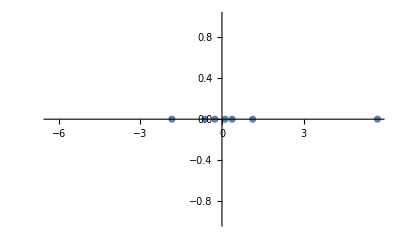

```mathematica
ListPlot[vals[[2]]]
```

```mathematica
CalculateAndDisplayRoots[k_, f_]:= Module[{vals},
vals = RootTestFunction2[k, f];
ListPlot[vals[[2]]]
];
```

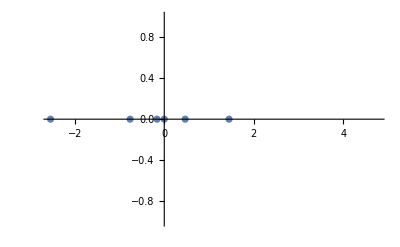

```mathematica
CalculateAndDisplayRoots[22,f2[1,t]]
```

```mathematica
vals = RootTestFunction2[10, f2[1,t]]
```

{2 z+4 z^2-z^3,{{-0.44949,0},{0.,0},{4.44949,0}},3}

```mathematica
ListPlot[vals[[2]]]
```

-Graphics-